```mathematica
data=First@Import["C:\\Users\\abduld\\Dropbox\\wbGPU\\survery_analysis\\Coursera Survey.xls"];
```

```mathematica
data[[2]]
```

{,Masters Degree,694.,,,1043.,1194.,7.76799,3.64139,3.50064,2.25257,3.94229,3.87752,3.83033,3.85094,3.91281,4.04683,3.27133,2.79511,3.11162,4.24768,3.70893,3.94183,4.15786,,}

```mathematica
education=data[[8;;,3]];
```

```mathematica
teducation=Tally[education];
```

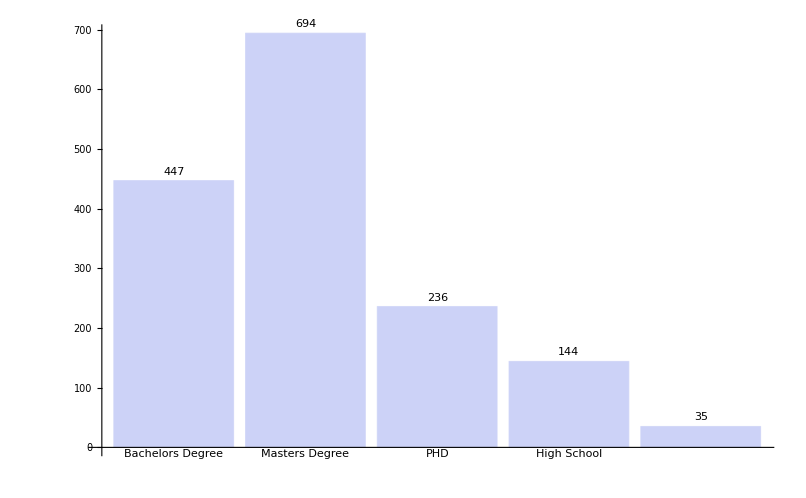

```mathematica
BarChart[Last/@teducation,ChartLabels->(First/@teducation),LabelingFunction->(Placed[Text[Style[#1,Medium]],Above]&)]
```

```mathematica
field=data[[8;;,5]];
```

```mathematica
tfield=Tally[field];
```

```mathematica
ClearAll[altName]
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("graphics")~~___]]="Visualization";
altName["Graphics"]="Visualization";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("electrical"|"electronic"|"electical")~~___]]="Electrical Engineering";
altName["EE"|"electrical engineering"]="Electrical Engineering";
altName["Mechanical Eng"]="Mechanical Engineering";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("phys"|"fem"|"cfd"|"phisics")~~___]]="Physics";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("biomed"|"bio-me"|"bioinf"|"bio")~~___]]="Biology";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("tel")~~___]]="Telecumunications";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("chem")~~___]]="Chemical Engineering";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("finance"|"econo")~~___]]="Finance";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("math"|"stat"|"numer")~~___]]="Mathematics";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("mech")~~___]]="Mechanical Engineering";altName["ME"]="Mechanical Engineering";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("indust")~~___]]="Industrial Engineering";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("nucl")~~___]]="Nuclear Engineering";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("aero")~~___]]="Aerospace Engineering";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("control")~~___]]="Control Systems";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("civil")~~___]]="Civil Engineering";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("info")~~___]]="Information Science";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("cs"|"comp"|"embed"|"image"|"cuda"|"software"|"computer"|"comput"|"develop"|"algo"|"programming"|"program"|"learning"|"hpc"|"parallel"|"robot"|"compiler"|"pattern"|"imag")~~___]]="Computer Science";
altName["it"|"CSE"|"CSEE"|"ECE"|"CS"|"IT"|"C"|"C++"|"C，C++"|"High Performance Computing"|"Artificial Intelligence"|"AI"|"Digital Image Processing"|"Image Processing"|"Networking"]="Computer Science";
altName[x_/;StringMatchQ[ToLowerCase[x],___~~("eng")~~___]]="Engineering";
altName[x___]:="Other";
```

```mathematica
ts=Reverse@SortBy[Tally[altName/@(First/@tfield)],Last];
```

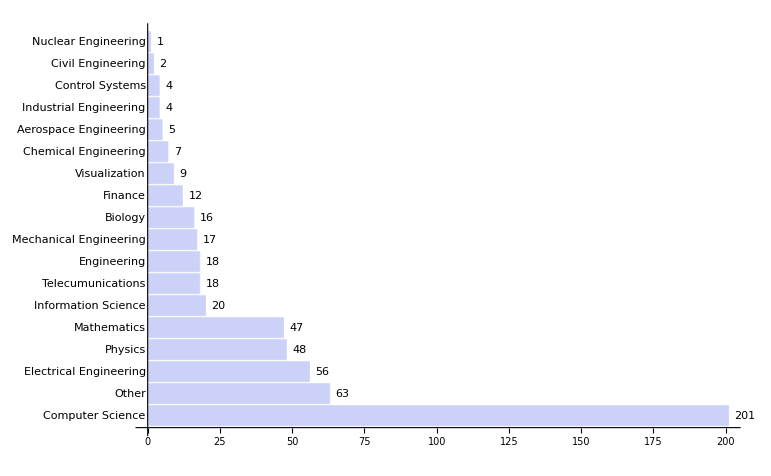

```mathematica
BarChart[Last/@ts,ChartLabels->(First/@ts),LabelingFunction->(Placed[Text[Style[#1,Medium]],After]&),BarOrigin->Left]
```